```mathematica
data=Import["/media/sajib/New Volume/New folder/MY WORKS AND DOCUMENTS/QED PROJECT/MY WORKS/Form Factors/720/form factor.csv"]
```

{{Q^2,GE,GM,GE Mon,GE Dip},{0.074195,0.7831,2.1849,0.905387,0.819726},{0.077316,0.7739,2.1592,0.901798,0.81324},{0.144645,0.6322,1.764,0.830754,0.690153},{0.18457,0.5609,1.5651,0.793677,0.629924},{0.0155,0.7497,2.0918,0.978635,0.957727},{0.01528,0.8906,2.4848,0.978932,0.958308},{0.016587,0.8799,2.4551,0.977171,0.954864},{0.017259,0.8745,2.4401,0.976268,0.9531},{0.040169,0.7353,2.0515,0.946453,0.895774},{0.015218,0.9216,2.5714,0.979016,0.958472},{0.016171,0.9175,2.56,0.977731,0.955958},{0.017171,0.9159,2.5556,0.976387,0.953331},{0.040309,0.8201,2.288,0.946277,0.89544},{0.074283,0.6916,1.9297,0.905285,0.819542},{0.07781,0.682,1.9028,0.901233,0.81222},{0.094418,0.6289,1.7547,0.882626,0.779028},{0.074309,0.753,2.1009,0.905255,0.819487},{0.094648,0.6975,1.9461,0.882373,0.778583}}

```mathematica
TableForm[data]
```

Q^2 | GE | GM | GE Mon | GE Dip
0.074195 | 0.7831 | 2.1849 | 0.905387 | 0.819726
0.077316 | 0.7739 | 2.1592 | 0.901798 | 0.81324
0.144645 | 0.6322 | 1.764 | 0.830754 | 0.690153
0.18457 | 0.5609 | 1.5651 | 0.793677 | 0.629924
0.0155 | 0.7497 | 2.0918 | 0.978635 | 0.957727
0.01528 | 0.8906 | 2.4848 | 0.978932 | 0.958308
0.016587 | 0.8799 | 2.4551 | 0.977171 | 0.954864
0.017259 | 0.8745 | 2.4401 | 0.976268 | 0.9531
0.040169 | 0.7353 | 2.0515 | 0.946453 | 0.895774
0.015218 | 0.9216 | 2.5714 | 0.979016 | 0.958472
0.016171 | 0.9175 | 2.56 | 0.977731 | 0.955958
0.017171 | 0.9159 | 2.5556 | 0.976387 | 0.953331
0.040309 | 0.8201 | 2.288 | 0.946277 | 0.89544
0.074283 | 0.6916 | 1.9297 | 0.905285 | 0.819542
0.07781 | 0.682 | 1.9028 | 0.901233 | 0.81222
0.094418 | 0.6289 | 1.7547 | 0.882626 | 0.779028
0.074309 | 0.753 | 2.1009 | 0.905255 | 0.819487
0.094648 | 0.6975 | 1.9461 | 0.882373 | 0.778583

```mathematica
p=data[[All,{1,4}]]
```

```mathematica
{{0.074195,0.905387052965143},{0.077316,0.901798007407445},{0.144645,0.830754289792838},{0.18457,0.793677409258079},{0.0155,0.978635423845624},{0.01528,0.978932274431944},{0.016587,0.977171350437043},{0.017259,0.976268427066561},{0.040169,0.946453399167388},{0.015218,0.979015964854706},{0.016171,0.977731140461406},{0.017171,0.976386572071769},{0.040309,0.946276800624809},{0.074283,0.905285464558074},{0.07781,0.901232530686333},{0.094418,0.882625699574102},{0.074309,0.905255454164111},{0.094648,0.882373410485082}}
```

```mathematica
q={{0.074195,0.905387052965143},{0.077316,0.901798007407445},{0.144645,0.830754289792838},{0.18457,0.793677409258079},{0.0155,0.978635423845624},{0.01528,0.978932274431944},{0.016587,0.977171350437043},{0.017259,0.976268427066561},{0.040169,0.946453399167388},{0.015218,0.979015964854706},{0.016171,0.977731140461406},{0.017171,0.976386572071769},{0.040309,0.946276800624809},{0.074283,0.905285464558074},{0.07781,0.901232530686333},{0.094418,0.882625699574102},{0.074309,0.905255454164111},{0.094648,0.882373410485082}}
```

{{0.074195,0.905387},{0.077316,0.901798},{0.144645,0.830754},{0.18457,0.793677},{0.0155,0.978635},{0.01528,0.978932},{0.016587,0.977171},{0.017259,0.976268},{0.040169,0.946453},{0.015218,0.979016},{0.016171,0.977731},{0.017171,0.976387},{0.040309,0.946277},{0.074283,0.905285},{0.07781,0.901233},{0.094418,0.882626},{0.074309,0.905255},{0.094648,0.882373}}

```mathematica
lm=LinearModelFit[q,{1,x,x^2},x]
```

FittedModel[0.999466-1.36985 x+1.38783 x^2]

```mathematica
lm["BestFit"]
```

0.999466-1.36985 x+1.38783 x^2

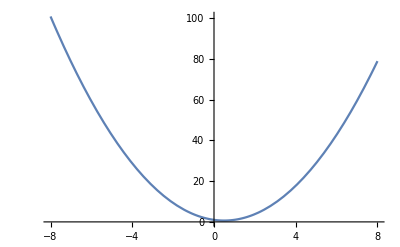

```mathematica
Plot[0.9994658067123545-1.3698509783393125 x+1.387828537827042 x^2,{x,-8,8}]
```

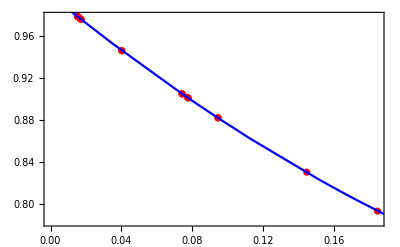

```mathematica
Show[ListPlot[q,PlotStyle->Red],Plot[0.9994658067123545-1.3698509783393125 x+1.387828537827042 x^2,{x,-8,8},PlotStyle->{Blue}],Frame->True]
```

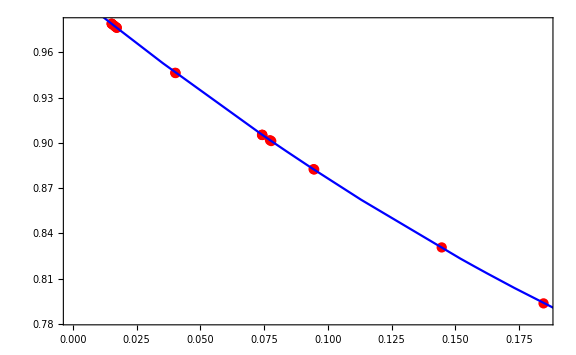

```mathematica
Show[%12,ImageSize->Large]
```

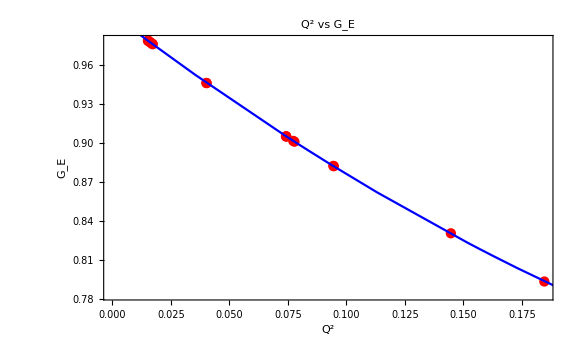

```mathematica
Show[%13,FrameLabel->{{HoldForm[Subscript["G", "E"]],None},{HoldForm[Q^2],None}},PlotLabel->HoldForm[Q^2 vs Subscript["G", "E"]],LabelStyle->{12,GrayLevel[0],Bold}]
```